# Prototyping - Video analysis

```mathematica
Quit[];
```

```mathematica
<<VideoTracking`
```

```mathematica
SelectVideo["~/Dropbox/PhD/Software/video-tracking/practice_videos/iScat_Bulk.avi"]
```

iScat_Bulk.avi has 1329 frames and is 720x480

```mathematica
SelectROI[({{373, 260}, {453, 260}, {453, 185}, {373, 185}})]
```

(373 | 260
453 | 260
453 | 185
373 | 185)

```mathematica
GetFrame[1]
```

-Graphics-

```mathematica
NumberOfFrames[]
```

1333

```mathematica
UpdateBackgroung[1,NumberOfFrames[]]
```

-Graphics-

```mathematica
CurrentBackground[]
```

{}

```mathematica
Options[VideoTracking]
```

{Threshold→Automatic,FilterArea→{9,40},FilterCircularity→{0.9,1.5},BufferSize→1000,UpdateBackgroung→False}

```mathematica
Binarize@SubstractBG[ GetFrame[ 7 ]]
```

-Graphics-

```mathematica
i1 =FrameBinarize[ SubstractBG[ GetFrame[ 7 ]]]
```

-Graphics-

```mathematica
SelectParticles[%]
```

{1,2}

```mathematica
AnalyseFrame[7]
```

Raw | Binirize | Img-BG, enhance
-Graphics- | -Graphics- | -Graphics-
frame→7
centroid→{1→{67.,8.5},2→{78.18,7.74}}
circularity→{1→1.15448,2→1.11479}
area→{1→26.5,2→25.875}
holes→{1→0,2→0}
results→{{67.,8.5},{78.18,7.74}}

```mathematica
GetPositions
```

```mathematica
SetOptions[VideoTracking, Threshold-> Automatic]
```

{Threshold→Automatic,FilterArea→{9,40},FilterCircularity→{0.9,1.5}}

```mathematica
OptionValue[VideoTracking, Threshold]
```

2

### Want to have: 1. Options based configuration of traking algorithm. 2. sub pixel tracking 3. MultiThreading

## 2. Sub pixel tracking

```mathematica
BoundParticleImg[img_,binImg_, id_Integer]:=ImageTrim[ img, (id/.ComponentMeasurements[binImg,"BoundingBox"]) ]
```

```mathematica
ImageToList[img_]:= Flatten[MapIndexed[{#2[[2]]-1,#2[[1]]-1,#1}&,Reverse[ImageData[img, "Byte"], 1],{2}],1]
```

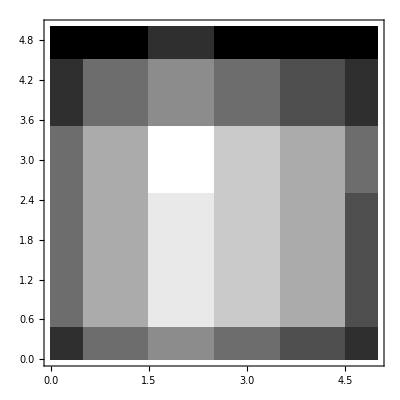

```mathematica
ListContourPlot[ ImageToList[img] , InterpolationOrder->0, ColorFunction->GrayLevel]
```

```mathematica
Reverse[ {{1,2,3} , {4,5,6},{7,8,9}}, 1]
```

(7 | 8 | 9
4 | 5 | 6
1 | 2 | 3)

```mathematica
SubPixel2DGaussianSimpleFit[img_]:= Module[ {data, fit, a,y,x,mx,my,b,s},
data = ImageToList[img] ;
fit =  NonlinearModelFit[data,a Exp@((-(-my+y)^2)/(2 s^2) -(-mx+x)^2/(2 s^2)),{{a,Max@data},{mx,ImageDimensions[img]⟦1⟧/2},{my,ImageDimensions[img]⟦2⟧/2},{s,3}},
{x,y}];
{"pos"->
{mx, my}/.fit["BestFitParameters"]
}
]
```

```mathematica
SubPixel2DGaussianFixedFit[img_]:= Module[ {data, fit, a,y,x,mx,my,b,sx,sy},
data = ImageToList[img] ;
fit =  NonlinearModelFit[data,a Exp@((-(-my+y)^2)/(2 sy^2) -(-mx+x)^2/(2 sx^2)),{{a,Max@data},{mx,ImageDimensions[img]⟦1⟧/2},{my,ImageDimensions[img]⟦2⟧/2},{sx,3},{sy,3}},
{x,y}];
{"pos"->
{mx, my}/.fit["BestFitParameters"]
}
]
```

```mathematica
img = BoundParticleImg[SubstractBG[ GetFrame[ 7 ]], i1,1]
```

-Graphics-

```mathematica
SubPixel2DGaussianSimpleFit[img]
pos/.%
ShowTrackOverlayed[img, %]
```

{pos→{2.37765,1.99031}}

{2.37765,1.99031}

-Graphics-

```mathematica
GetPositions[i1]
```

(66.9615 | 8.65385
78.2 | 7.8)

```mathematica
ComponentMeasurements[i1,"BoundingBox"]
```

{1→{{65.,7.},{69.,11.}},2→{{76.,6.},{80.,10.}}}

```mathematica
ShowTrackOverlayed[img_,list_]:=Show[img,
Graphics@Flatten@{Red,Point[#]&/@list}, 
ImageSize -> Large]
```

```mathematica
FitSubPixel[img_, box_]:= ("pos"/.SubPixel2DGaussianFixedFit[ ImageTrim[ img, box ] ]) + box[[1]]
```

```mathematica
ForFitSubPixel[img_,binImg_, ids_]:=FitSubPixel[img,#]&/@ (ids /. ComponentMeasurements[binImg,"BoundingBox"])
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

(2.00009 | 1341.4)

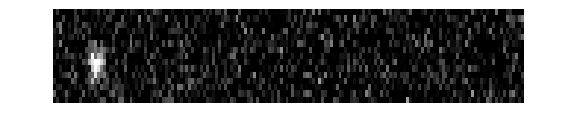

(9.22727 | 12.2273
45.0556 | 8.83333
125.864 | 9.5
62.1667 | 6.61111
48.9 | 3.6
39. | 1.8)

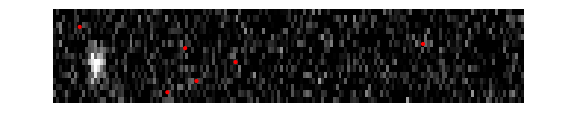

```mathematica
img  = img4;
imgWBG = img4;

ForFitSubPixel[
img, 
FrameBinarize[ imgWBG ], 
{1}]

ShowTrackOverlayed[ img, %]

GetPositions[ FrameBinarize[ imgWBG ]] 
ShowTrackOverlayed[ img, %]
```

### Test Image

```mathematica
dataTest=Round[  255 Table[ Exp[ (- ((16-h)- 6.7)^2)/(2 2^2)-(w-15.3)^2/(2 2^2)], {h,1,15}, {w,1,160}] ];
img4= (Image[dataTest, "Byte"]) ~ ImageEffect ~ {"GaussianNoise",0.2}
```

-Graphics-

```mathematica
ImageToList@-Graphics-
```

```mathematica
GetFrame[ lookAt ] // ImageDimensions
```

{161,15}

```mathematica
SubPixelShow[img_, fns_]:= Show[
Graphics[
Inset[img, {-0.5,-0.5},{Left,Bottom}, img//ImageDimensions]
],

Graphics@Flatten[ 
{RandomColor[],Tooltip[Point[pos/.#@img],#] &/@ fns}
],

ImageSize -> Medium
]
```

```mathematica
SubPixelShow[img, {SubPixel2DGaussianSimpleFit}]
```

-Graphics-

```mathematica
f[x_]:=Module[{},
a = 1;
If[x===1, Return[1]];
3]
```

```mathematica
f[3]
```

3

```mathematica
OptionValue[Plot, 20, 1]
```

OptionValue::rep: 20 is not a valid replacement rule.

OptionValue::optnf: Option name 1 not found in defaults for Plot.

1

```mathematica
Ceiling[1.1]
```

2

```mathematica
from = 1100;
to =  2501;
buffer = 1000;

Ceiling[to,buffer] - Ceiling[from,buffer]< buffer

from
Ceiling[from,buffer]

Min[ Ceiling[from,buffer]+1 , to]
to
```

False

1100

2000

2001

2501

```mathematica
Ceiling[to,buffer]
```

3000

## Lets run the analysis!

```mathematica
i=1;
AnalyseFrame[i]

ShowTrackOverlayed[ GetFrame[i], %]
```

(67.7618 | 8.28603
79.5773 | 9.26234)

-Graphics-

```mathematica
Unzipper[el_]:=If[Length@el[[2]]>0,Map[{el[[1]],#}&,el[[2]]],{}]
```

```mathematica
Unzipper[ {1,{{2,3},{4,5},{6,7}}}]
```

{{1,{2,3}},{1,{4,5}},{1,{6,7}}}

```mathematica
Quit[];
```

```mathematica
<<VideoTracking`

SelectVideo["~/Dropbox/PhD/Software/video-tracking/practice_videos/video_2.avi"]

SelectROI[({{291, 140}, {451, 140}, {451, 126}, {291, 126}})]

UpdateBackgroung[1,NumberOfFrames[]]
```

video_2.avi has 1333 frames and is 720x480

(291 | 140
451 | 140
451 | 126
291 | 126)

-Graphics-

```mathematica
GetFrame[1]
```

-Graphics-

```mathematica
out = RunAnalysis[] // AbsoluteTiming
```

{47.42494,{{1,67.7618,8.28603},{1,79.5773,9.26234},2663,{1333,119.778,7.84597}}}
 |  |  |  |

unparallel execution took ~41.3945 and parallel took 41.389065 

⇒ seems to be diffrent only in initiation 

second time the same:
parallel: 27.24 sec
unparallel 26.8 sec

⇒ keep for now just because might work on better computer

In future need to optimese this by having less globals?

```mathematica
40.3945 sec
```

40.3945 sec

```mathematica
MemoryInUse[] / 1000000 //N
```

112.916

## New buffer testing

```mathematica
<<VideoIO`
```

```mathematica
AskBufferFor[1]
```

```mathematica
Length@VideoIO`Private`bufferVideo
```

401

```mathematica
VideoIO`Private`bufferRange
```

{-399,401}

```mathematica
VideoIO`Private`bufferSizeN // Floor
```

1446

```mathematica
GetFrame[1000]
```

Loading: buffer append with new files. Buffer: {1, 801}

Loading: buffer append with new files. Buffer: {1, 1201}

-Graphics-

```mathematica
i =1220;
ImageDifference[ GetFrames[i][[1]] , GetFrame[i] ] // ImageAdjust
```

Loading: buffer append with new files. Buffer: {1, 1329}

-Graphics-

```mathematica
StatusArea["label"]
```

label